```mathematica
FindRoot[LogIntegral[x]-Log[Log[x]]-EulerGamma==1,{x,2}]
```

{x→2.23525}

```mathematica
LogIntegral[2.235248176511392]-Log@Log@2.235248176511392-EulerGamma
```

1.

```mathematica
Clear[bin,co,gg]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
co[a_, s_] := co[a,s]=Limit[ D[Log[x+1]^a/s!,{x,s}],x->0]
gg[n_, k_] := gg[n,k]=(-1)^k Gamma[ k,0,-Log[n]]/Gamma[k]
gga[n_, k_] := (-1)^k gs[ k,ln]/Gamma[k]
```

```mathematica
Table[ co[2,s],{s,0,10}]
```

{0,0,1,-1,11/12,-5/6,137/180,-7/10,363/560,-761/1260,7129/12600}

```mathematica
Series[ Log[x+1]^3,{x,0,10}]
```

x^3-(3 x^4)/2+(7 x^5)/4-(15 x^6)/8+(29 x^7)/15-(469 x^8)/240+(29531 x^9)/15120-(1303 x^10)/672+O[x]^11

```mathematica
pp[n_, a_, t_] := Sum[ co[a,s]gg[n,s],{s,1,t}]
pa[n_, a_, t_] := 1+Sum[ bin[z,s]gga[n,s],{s,1,t}]
```

```mathematica
Chop@N@pp[2.235248176511392,1,50.]
```

1.

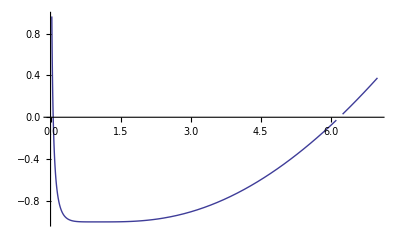

```mathematica
Plot[ pp[n,4,80.]-1,{n,0,7}]
```

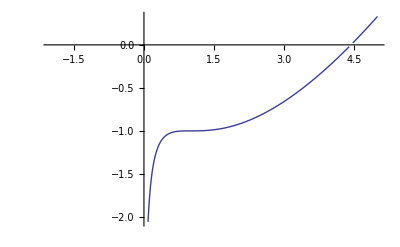

```mathematica
Plot[ pp[n,3,80.]-1,{n,-2,5}]
```

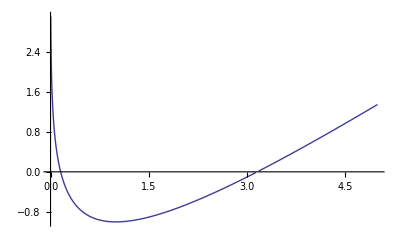

```mathematica
Plot[ pp[n,2,80.]-1,{n,0,5}]
```

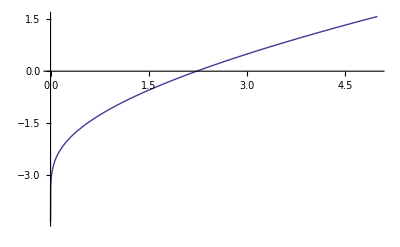

```mathematica
Plot[ pp[n,1,80.]-1,{n,0,5}]
```

```mathematica
N@D[LaguerreL[-z,Log[100]],{z,1}]/.z->0
```

28.0217

```mathematica
Table[{(-1)^k / (k!) Binomial[ -z, k],Binomial[z+k-1, k]/k!,Gamma[k+z]/(Gamma[1+k]^2 Gamma[z])},{k,0,6}]/.{z->5}//TableForm
```

1 | 1 | 1
5 | 5 | 5
15/2 | 15/2 | 15/2
35/6 | 35/6 | 35/6
35/12 | 35/12 | 35/12
21/20 | 21/20 | 21/20
7/24 | 7/24 | 7/24

```mathematica
FullSimplify[(z+k-1)!/((((z+k-1)-(k))!)((k)!)((k)!))]
```

Gamma[k+z]/(Gamma[1+k]^2 Gamma[z])

```mathematica
Expand@D[pa[n,1,7],z]
```

-gs[1,ln]-1/2 gs[2,ln]+z gs[2,ln]-1/6 gs[3,ln]+1/2 z gs[3,ln]-1/4 z^2 gs[3,ln]-1/24 gs[4,ln]+11/72 z gs[4,ln]-1/8 z^2 gs[4,ln]+1/36 z^3 gs[4,ln]-1/120 gs[5,ln]+5/144 z gs[5,ln]-7/192 z^2 gs[5,ln]+1/72 z^3 gs[5,ln]-1/576 z^4 gs[5,ln]-1/720 gs[6,ln]+(137 z gs[6,ln])/21600-1/128 z^2 gs[6,ln]+(17 z^3 gs[6,ln])/4320-(z^4 gs[6,ln])/1152+(z^5 gs[6,ln])/14400-gs[7,ln]/5040+(7 z gs[7,ln])/7200-(29 z^2 gs[7,ln])/21600+(7 z^3 gs[7,ln])/8640-(5 z^4 gs[7,ln])/20736+(z^5 gs[7,ln])/28800-(z^6 gs[7,ln])/518400

```mathematica
1+Integrate[ Log[x]x^y,{y,0,n}]
```

x^n

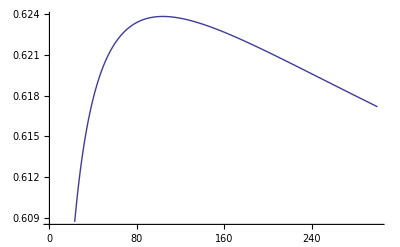

```mathematica
Plot[ pp[n,2,50]/pp[n,1,50.]/Log[n],{n,1,300}]
```

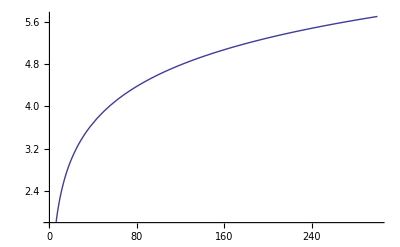

```mathematica
Plot[ Log[n],{n,1,300}]
```

```mathematica
D[Binomial[z,k],{z,2}]
```

Binomial[z,k] (PolyGamma[0,1+z]-PolyGamma[0,1-k+z])^2+Binomial[z,k] (PolyGamma[1,1+z]-PolyGamma[1,1-k+z])

```mathematica
Table[ Binomial[z,k] (PolyGamma[0,1+z]-PolyGamma[0,1-k+z])^2+Binomial[z,k] (PolyGamma[1,1+z]-PolyGamma[1,1-k+z])(-1)^k / k!,{k,0,5}]//TableForm
```

0
z (-PolyGamma[0,z]+PolyGamma[0,1+z])^2-z (-PolyGamma[1,z]+PolyGamma[1,1+z])
1/2 (-1+z) z (-PolyGamma[0,-1+z]+PolyGamma[0,1+z])^2+1/4 (-1+z) z (-PolyGamma[1,-1+z]+PolyGamma[1,1+z])
1/6 (-2+z) (-1+z) z (-PolyGamma[0,-2+z]+PolyGamma[0,1+z])^2-1/36 (-2+z) (-1+z) z (-PolyGamma[1,-2+z]+PolyGamma[1,1+z])
1/24 (-3+z) (-2+z) (-1+z) z (-PolyGamma[0,-3+z]+PolyGamma[0,1+z])^2+1/576 (-3+z) (-2+z) (-1+z) z (-PolyGamma[1,-3+z]+PolyGamma[1,1+z])
1/120 (-4+z) (-3+z) (-2+z) (-1+z) z (-PolyGamma[0,-4+z]+PolyGamma[0,1+z])^2-((-4+z) (-3+z) (-2+z) (-1+z) z (-PolyGamma[1,-4+z]+PolyGamma[1,1+z]))/14400

```mathematica
a Integrate[ D[y^(a-1),y],{y,0,x}]
```

ConditionalExpression[a x^(-1+a),Re[a]>1]

```mathematica
D[x^a,x]
```

a x^(-1+a)

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=Product[(-1)^p[[2]] bin[-z,p[[2]]],{p,FI[n]}]
Dz[n_, z_] := Sum[ dz[j,z],{j,1,n}]
d2[n_, a_, b_] := Sum[dz[j,a]dz[k,b],{j,1,n},{k,1,n/j}]-Sum[dz[j,a]dz[k,b],{j,1,n-1},{k,1,(n-1)/j}]
d2a[n_, a_] := Sum[dz[j,a]dz[k,1],{j,1,n},{k,1,n/j}]-Sum[dz[j,a]dz[k,1],{j,1,n-1},{k,1,(n-1)/j}]
d2b[n_, a_] := Sum[dz[j,a],{j,1,n},{k,1,n/j}]-Sum[dz[j,a],{j,1,n-1},{k,1,(n-1)/j}]
d2c[n_, a_] := Sum[dz[j,a] Sum[ 1,{k,1,n/j}],{j,1,n}]-Sum[dz[j,a] Sum[ 1,{k,1,(n-1)/j}],{j,1,n-1}]
d2d[n_, a_] := Sum[dz[j,a] Floor[n/j],{j,1,n}]-Sum[dz[j,a] Floor[(n-1)/j],{j,1,n-1}]
d2e[n_, a_] := Sum[dz[j,a] Floor[n/j],{j,1,n-1}]+Sum[dz[j,a] Floor[n/j],{j,n,n}]-Sum[dz[j,a] Floor[(n-1)/j],{j,1,n-1}]
d2f[n_, a_] := Sum[dz[j,a] Floor[n/j],{j,1,n-1}]+dz[n,a] -Sum[dz[j,a] Floor[(n-1)/j],{j,1,n-1}]
d2g[n_, a_] := dz[n,a]+Sum[dz[j,a] Floor[n/j]-dz[j,a] Floor[(n-1)/j],{j,1,n-1}]
d2h[n_, a_] := dz[n,a]+Sum[dz[j,a] (Floor[n/j]- Floor[(n-1)/j]),{j,1,n-1}]
```

```mathematica
d2h[98,4]
```

75

```mathematica
D[1,x]
```

0

```mathematica
FullSimplify@D[ Integrate[ D[ LaguerreL[-a, Log[x]],x],{x,1,n}],n]
```

ConditionalExpression[(a Hypergeometric1F1[1+a,2,Log[n]])/n,0≤Re[n]≤ⅇ||n∉Reals]

```mathematica
FullSimplify@D[ Integrate[ D[ LaguerreL[-b, Log[y]],y],{y,1,n}],n]
```

ConditionalExpression[(b Hypergeometric1F1[1+b,2,Log[n]])/n,0≤Re[n]≤ⅇ||n∉Reals]

```mathematica
FullSimplify@D[ Integrate[D[ LaguerreL[-a, Log[x]],x] D[ LaguerreL[-b, Log[y]],y],{x,1,n},{y,1,n/x}],n]
```

∫_1^n (a b Hypergeometric1F1[1+a,2,Log[x]] Hypergeometric1F1[1+b,2,Log[n/x]])/(n x)ⅆx

```mathematica
N[(a Hypergeometric1F1[1+a,2,Log[n]])/n+(b Hypergeometric1F1[1+b,2,Log[n]])/n+∫_1^n (a b Hypergeometric1F1[1+a,2,Log[x]] Hypergeometric1F1[1+b,2,Log[n/x]])/(n x)ⅆx/.{a->3,b->2,n->10}]
```

65.88

```mathematica
N[D[LaguerreL[-3-2,Log[n]],n]/.n->10]
```

65.88

```mathematica
Integrate[ D[ LaguerreL[-a, Log[x]],x],{x,1,n}]
```

```mathematica
ConditionalExpression[-1+Hypergeometric1F1[a,1,Log[n]],0≤Re[n]≤ⅇ||n∉Reals
```

```mathematica
Integrate[ D[ LaguerreL[-a, Log[x]],x],{x,1,n}]
```

ConditionalExpression[-1+Hypergeometric1F1[a,1,Log[n]],0≤Re[n]≤ⅇ||n∉Reals]

```mathematica
D[Integrate[ D[ LaguerreL[-1, Log[y]],y],{y,1,n}],n]
```

1

```mathematica
D[Integrate[ D[ LaguerreL[-a, Log[x]],x](n/x),{x,1,n}],n]
```

∫_1^n -LaguerreL[-1-a,1,Log[x]]/x^2ⅆx-LaguerreL[-1-a,1,Log[n]]/n

```mathematica
FullSimplify@D[ Integrate[D[ LaguerreL[-a, Log[x]],x] ,{x,1,n},{y,1,n/x}],n]
```

∫_1^n (a Hypergeometric1F1[1+a,2,Log[x]])/x^2 ⅆx

```mathematica
N[1+(a Hypergeometric1F1[1+a,2,Log[n]])/n+∫_1^n -LaguerreL[-1-a,1,Log[x]]/x^2 ⅆx/.{a->4,n->10}]
```

65.88

```mathematica
N[1+∫_1^n -LaguerreL[-1-a,1,Log[x]]/x^2 ⅆx-LaguerreL[-1-a,1,Log[n]]/n/.{a->4,n->10}]
```

65.88

```mathematica
Integrate[- (a Hypergeometric1F1[1+a,2,Log[x]])/x^2,{x,1,n}]
```

∫_1^n -(a Hypergeometric1F1[1+a,2,Log[x]])/x^2ⅆx

```mathematica
n Integrate[ D[ LaguerreL[-a, Log[x]],x]/x,{x,1,n}]
```

n ∫_1^n -LaguerreL[-1-a,1,Log[x]]/x^2ⅆx

```mathematica
D[ LaguerreL[-a, Log[x]],x]
```

-LaguerreL[-1-a,1,Log[x]]/x

```mathematica
D[ Gamma[k,0,-Log[n]],n]
```

-(-Log[n])^(-1+k)

```mathematica
-(-Log[n])^(-1+k)/.{k->5,n->20}
```

-Log[20]^4

```mathematica
(-1)^(k)( Log[n])^(-1+k)/.{k->5,n->20}
```

-Log[20]^4

```mathematica
Sum[ bin[z,k] Log[n]^(k-1)/((k-1)!),{k,0,Infinity}]
```

z Hypergeometric1F1[1-z,2,-Log[n]]

```mathematica
Sum[ (-1)^k/k Log[n]^(k-1)/Gamma[k],{k,1,Infinity}]
```

(1-n)/(n Log[n])

```mathematica
D[z Hypergeometric1F1[1-z,2,-Log[n]],{z,1}]/.z->0
```

(-1+n)/(n Log[n])

```mathematica
ff[z_] := Sum[ Binomial[z,k]Log[n]^(k-1)/((k-1)!),{k,1,z}]
```

```mathematica
ff[6]
```

6+15 Log[n]+10 Log[n]^2+(5 Log[n]^3)/2+Log[n]^4/4+Log[n]^5/120

```mathematica
N[-2 Derivative[1,0,0][Hypergeometric1F1][1,2,-Log[n]]/.n->20]
```

0.851865

```mathematica
-2D[Pochhammer[1-z,k] (-Log[n])^k / (Pochhammer[2,k] k!),z]/.z->0
```

(2 (-Log[n])^k Pochhammer[1,k] (EulerGamma+PolyGamma[0,1+k]))/(k! Pochhammer[2,k])

```mathematica
(2 (-Log[n])^k Pochhammer[1,k] (EulerGamma+PolyGamma[0,1+k]))/(k! Pochhammer[2,k])/.k->5
```

-(137 Log[n]^5)/21600

```mathematica
(2 (-1)^k Pochhammer[1,k] (EulerGamma+PolyGamma[0,1+k]))/(k! Pochhammer[2,k])/.k->5
```

-137/21600

```mathematica
FullSimplify[(2 (-1)^k Pochhammer[1,k] (EulerGamma+PolyGamma[0,1+k]))/(k! Pochhammer[2,k])]
```

(2 (-1)^k HarmonicNumber[k])/Gamma[2+k]

```mathematica
-2 Sum[ ((-1)^k HarmonicNumber[k])/Gamma[2+k] Log[n]^k,{k,0,Infinity}]
```

-2 Hypergeometric1F1^(1,0,0)[1,2,-Log[n]]

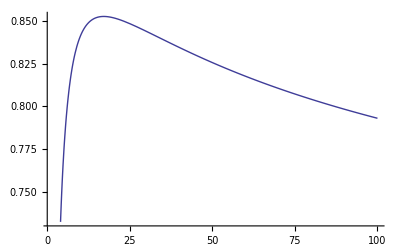

```mathematica
Plot[ -2 Derivative[1,0,0][Hypergeometric1F1][1,2,-Log[n]], {n,1,100}]
```

```mathematica
Integrate[ -2 Derivative[1,0,0][Hypergeometric1F1][1,2,-Log[x]], {x,0,n}]
```

∫_0^n -2 Hypergeometric1F1^(1,0,0)[1,2,-Log[x]]ⅆx

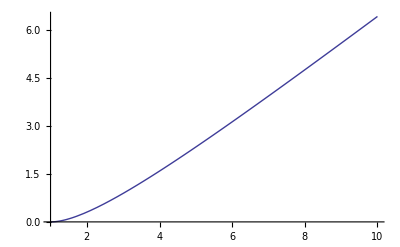

```mathematica
Plot[ ∫_1^n -2 Derivative[1,0,0][Hypergeometric1F1][1,2,-Log[x]]ⅆx, {n,1,10}]
```

```mathematica
Plot[ pp[n,2,30.],{n,1,10}]
```

-Graphics-

```mathematica
D[z Hypergeometric1F1[1-z,2,-Log[n]],{z,1}]/.z->0
```

(-1+n)/(n Log[n])

```mathematica
D[z^2 Hypergeometric1F1[1-z,2,-Log[n]],{z,2}]/.z->0
```

(2 (-1+n))/(n Log[n])

```mathematica
Integrate[ 1/Log[n]-1/(n Log[n]),{n,1,x}]
```

ConditionalExpression[-EulerGamma-Gamma[0,-Log[x]]-Log[-Log[x]],Im[x]≠0||Re[x]≥0]

```mathematica
Limit[(2 (-1+n))/(n Log[n]),n->1]
```

2

```mathematica
FullSimplify[(2 (-1+n))/(n Log[n])-(1/Log[n] - 2/(n Log[n]) + 1/(n^2 Log[n]))]
```

(-1+n^2)/(n^2 Log[n])

```mathematica
Limit[ (-1+n^2)/(n^2 Log[n])-((-1+n)/(n Log[n])),n->1]
```

1

```mathematica
Integrate[  (-1+n^k)/(n^k Log[n]),n]
```

-ExpIntegralEi[-(-1+k) Log[n]]+LogIntegral[n]

```mathematica
Limit[ (-1+n^k)/(n^k Log[n])- (-1+n^(k-1))/(n^(k-1) Log[n]),n->1]
```

1

```mathematica
ff[n_, k_] :=  (-1+n^k)/(n^k Log[n])- (-1+n^(k-1))/(n^(k-1) Log[n])
```

```mathematica
Plot[ ff[n,0],{n,0,5}]
```

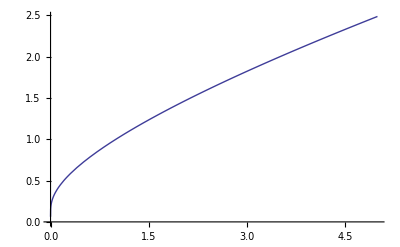

```mathematica
FullSimplify[ff[n,3]]
```

(-1+n)/(n^3 Log[n])

```mathematica
D[x^z,{z,2}]/.z->0
```

Log[x]^2

```mathematica
Integrate[ z Hypergeometric1F1[1-z,2,-Log[n]],{n,1,x}]
```

∫_1^x z Hypergeometric1F1[1-z,2,-Log[n]]ⅆn

```mathematica
N[1+Integrate[ z Hypergeometric1F1[1-z,2,-Log[n]],{n,1,x}]/.{x->10,z->2}]
```

33.0259

```mathematica
N[LaguerreL[-2,Log[10]]]
```

33.0259

```mathematica
N[Hypergeometric1F1[2,1,Log[10]]]
```

33.0259

```mathematica
FullSimplify[(1+n)! / (1! n!)]
```

1+n

```mathematica
N[ D[ LaguerreL[ -z, Log[n]],n]/.{n->16,z->3}]
```

15.1614

```mathematica
N[(-z/Log[n])( LaguerreL[ -z,Log[n]] -  LaguerreL[-z-1,Log[n]])/n/.{n->16,z->3}]
```

15.1614

```mathematica
N@D[ LaguerreL[ z,Log[n]],n]/.{z->-3, n->16}
```

15.1614

```mathematica
D[ fa[Log[x]],x]
```

fa'[Log[x]]/x

```mathematica
FullSimplify[(-z/Log[n])( LaguerreL[ -z,Log[n]] -  LaguerreL[-z-1,Log[n]])/n]
```

(z (-Hypergeometric1F1[z,1,Log[n]]+Hypergeometric1F1[1+z,1,Log[n]]))/(n Log[n])

```mathematica
(z/(n Log[n]))( LaguerreL[-z-1,Log[n]]-LaguerreL[ -z,Log[n]])
```

```mathematica
(z (LaguerreL[-1-z,Log[n]]-LaguerreL[-z,Log[n]]))/(n Log[n])
```

```mathematica
N[1+ Integrate[ z/(x Log[x]) (LaguerreL[-z-1, Log[x]]-LaguerreL[-z,Log[x]]),{x,1,n}]/.{z->3,n->12}]
```

108.686+0. ⅈ

```mathematica
N[LaguerreL[-3,Log[12]]]
```

108.686

```mathematica
N[1+ Integrate[ z Hypergeometric1F1[1-z,2,-Log[x]],{x,1,n}]/.{z->3,n->12}]
```

108.686

```mathematica
LaguerreL[0,n]
```

1

```mathematica
N[Integrate[ D[LaguerreL[-z,Log[r]],r]/.r->x,{x,1,n}]/.{z->3,n->12}]
```

Undefined

```mathematica
N@LaguerreL[-3,Log[12]]
```

108.686